```mathematica
<<getFeigenbaum`

rInv={0,2};
f[r_,x_]:=1-r*x^2;
p=getFeigenbaum[f,rInv,4,15];
eventualOrbit[r_,x0_]:=NestList[f[r,#]&,x0,10^7];
```

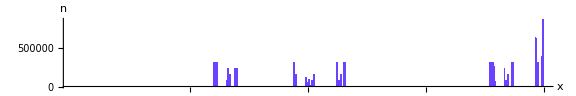

```mathematica
Histogram[eventualOrbit[p[[15,1]],0.5],{-1,1,4/1000},"Count",ImageSize->Large,AxesLabel->{x,n},ChartStyle->RGBColor[0.42,0.26,1],AspectRatio->1/6,Ticks->{{-0.5,0,0.5,1},Automatic}]
```

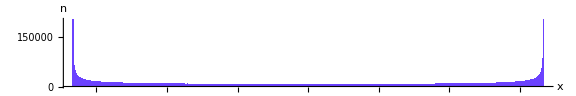

```mathematica
Histogram[eventualOrbit[2,0.2],{-1,1,2/1000},"Count",ImageSize->Large,AxesLabel->{x,n},ChartStyle->RGBColor[0.42,0.26,1],AspectRatio->1/6]
```